```mathematica
Clear[y]
```

```mathematica
L=2.
```

2.

```mathematica
M=100;
```

```mathematica
Δx=L/M
```

0.02

```mathematica
x[j_]= j Δx;
```

```mathematica
c[x_]=1+x;
```

```mathematica
y[0][t_]=0;
y[M][t_]=0;
```

```mathematica
vars=Table[y[j],{j,1,M-1}]
```

{y[1],y[2],y[3],y[4],y[5],y[6],y[7],y[8],y[9],y[10],y[11],y[12],y[13],y[14],y[15],y[16],y[17],y[18],y[19],y[20],y[21],y[22],y[23],y[24],y[25],y[26],y[27],y[28],y[29],y[30],y[31],y[32],y[33],y[34],y[35],y[36],y[37],y[38],y[39],y[40],y[41],y[42],y[43],y[44],y[45],y[46],y[47],y[48],y[49],y[50],y[51],y[52],y[53],y[54],y[55],y[56],y[57],y[58],y[59],y[60],y[61],y[62],y[63],y[64],y[65],y[66],y[67],y[68],y[69],y[70],y[71],y[72],y[73],y[74],y[75],y[76],y[77],y[78],y[79],y[80],y[81],y[82],y[83],y[84],y[85],y[86],y[87],y[88],y[89],y[90],y[91],y[92],y[93],y[94],y[95],y[96],y[97],y[98],y[99]}

```mathematica
eqs=Table[y[j]''[t]==c[x[j]]^2 (y[j+1][t]-2y[j][t]+y[j-1][t])/Δx^2,{j,1,M-1}]
```

{y[1]''[t]==2601. (-2 y[1][t]+y[2][t]),y[2]''[t]==2704. (y[1][t]-2 y[2][t]+y[3][t]),y[3]''[t]==2809. (y[2][t]-2 y[3][t]+y[4][t]),y[4]''[t]==2916. (y[3][t]-2 y[4][t]+y[5][t]),y[5]''[t]==3025. (y[4][t]-2 y[5][t]+y[6][t]),y[6]''[t]==3136. (y[5][t]-2 y[6][t]+y[7][t]),y[7]''[t]==3249. (y[6][t]-2 y[7][t]+y[8][t]),y[8]''[t]==3364. (y[7][t]-2 y[8][t]+y[9][t]),y[9]''[t]==3481. (y[8][t]-2 y[9][t]+y[10][t]),y[10]''[t]==3600. (y[9][t]-2 y[10][t]+y[11][t]),y[11]''[t]==3721. (y[10][t]-2 y[11][t]+y[12][t]),y[12]''[t]==3844. (y[11][t]-2 y[12][t]+y[13][t]),y[13]''[t]==3969. (y[12][t]-2 y[13][t]+y[14][t]),y[14]''[t]==4096. (y[13][t]-2 y[14][t]+y[15][t]),y[15]''[t]==4225. (y[14][t]-2 y[15][t]+y[16][t]),y[16]''[t]==4356. (y[15][t]-2 y[16][t]+y[17][t]),y[17]''[t]==4489. (y[16][t]-2 y[17][t]+y[18][t]),y[18]''[t]==4624. (y[17][t]-2 y[18][t]+y[19][t]),y[19]''[t]==4761. (y[18][t]-2 y[19][t]+y[20][t]),y[20]''[t]==4900. (y[19][t]-2 y[20][t]+y[21][t]),y[21]''[t]==5041. (y[20][t]-2 y[21][t]+y[22][t]),y[22]''[t]==5184. (y[21][t]-2 y[22][t]+y[23][t]),y[23]''[t]==5329. (y[22][t]-2 y[23][t]+y[24][t]),y[24]''[t]==5476. (y[23][t]-2 y[24][t]+y[25][t]),y[25]''[t]==5625. (y[24][t]-2 y[25][t]+y[26][t]),y[26]''[t]==5776. (y[25][t]-2 y[26][t]+y[27][t]),y[27]''[t]==5929. (y[26][t]-2 y[27][t]+y[28][t]),y[28]''[t]==6084. (y[27][t]-2 y[28][t]+y[29][t]),y[29]''[t]==6241. (y[28][t]-2 y[29][t]+y[30][t]),y[30]''[t]==6400. (y[29][t]-2 y[30][t]+y[31][t]),y[31]''[t]==6561. (y[30][t]-2 y[31][t]+y[32][t]),y[32]''[t]==6724. (y[31][t]-2 y[32][t]+y[33][t]),y[33]''[t]==6889. (y[32][t]-2 y[33][t]+y[34][t]),y[34]''[t]==7056. (y[33][t]-2 y[34][t]+y[35][t]),y[35]''[t]==7225. (y[34][t]-2 y[35][t]+y[36][t]),y[36]''[t]==7396. (y[35][t]-2 y[36][t]+y[37][t]),y[37]''[t]==7569. (y[36][t]-2 y[37][t]+y[38][t]),y[38]''[t]==7744. (y[37][t]-2 y[38][t]+y[39][t]),y[39]''[t]==7921. (y[38][t]-2 y[39][t]+y[40][t]),y[40]''[t]==8100. (y[39][t]-2 y[40][t]+y[41][t]),y[41]''[t]==8281. (y[40][t]-2 y[41][t]+y[42][t]),y[42]''[t]==8464. (y[41][t]-2 y[42][t]+y[43][t]),y[43]''[t]==8649. (y[42][t]-2 y[43][t]+y[44][t]),y[44]''[t]==8836. (y[43][t]-2 y[44][t]+y[45][t]),y[45]''[t]==9025. (y[44][t]-2 y[45][t]+y[46][t]),y[46]''[t]==9216. (y[45][t]-2 y[46][t]+y[47][t]),y[47]''[t]==9409. (y[46][t]-2 y[47][t]+y[48][t]),y[48]''[t]==9604. (y[47][t]-2 y[48][t]+y[49][t]),y[49]''[t]==9801. (y[48][t]-2 y[49][t]+y[50][t]),y[50]''[t]==10000. (y[49][t]-2 y[50][t]+y[51][t]),y[51]''[t]==10201. (y[50][t]-2 y[51][t]+y[52][t]),y[52]''[t]==10404. (y[51][t]-2 y[52][t]+y[53][t]),y[53]''[t]==10609. (y[52][t]-2 y[53][t]+y[54][t]),y[54]''[t]==10816. (y[53][t]-2 y[54][t]+y[55][t]),y[55]''[t]==11025. (y[54][t]-2 y[55][t]+y[56][t]),y[56]''[t]==11236. (y[55][t]-2 y[56][t]+y[57][t]),y[57]''[t]==11449. (y[56][t]-2 y[57][t]+y[58][t]),y[58]''[t]==11664. (y[57][t]-2 y[58][t]+y[59][t]),y[59]''[t]==11881. (y[58][t]-2 y[59][t]+y[60][t]),y[60]''[t]==12100. (y[59][t]-2 y[60][t]+y[61][t]),y[61]''[t]==12321. (y[60][t]-2 y[61][t]+y[62][t]),y[62]''[t]==12544. (y[61][t]-2 y[62][t]+y[63][t]),y[63]''[t]==12769. (y[62][t]-2 y[63][t]+y[64][t]),y[64]''[t]==12996. (y[63][t]-2 y[64][t]+y[65][t]),y[65]''[t]==13225. (y[64][t]-2 y[65][t]+y[66][t]),y[66]''[t]==13456. (y[65][t]-2 y[66][t]+y[67][t]),y[67]''[t]==13689. (y[66][t]-2 y[67][t]+y[68][t]),y[68]''[t]==13924. (y[67][t]-2 y[68][t]+y[69][t]),y[69]''[t]==14161. (y[68][t]-2 y[69][t]+y[70][t]),y[70]''[t]==14400. (y[69][t]-2 y[70][t]+y[71][t]),y[71]''[t]==14641. (y[70][t]-2 y[71][t]+y[72][t]),y[72]''[t]==14884. (y[71][t]-2 y[72][t]+y[73][t]),y[73]''[t]==15129. (y[72][t]-2 y[73][t]+y[74][t]),y[74]''[t]==15376. (y[73][t]-2 y[74][t]+y[75][t]),y[75]''[t]==15625. (y[74][t]-2 y[75][t]+y[76][t]),y[76]''[t]==15876. (y[75][t]-2 y[76][t]+y[77][t]),y[77]''[t]==16129. (y[76][t]-2 y[77][t]+y[78][t]),y[78]''[t]==16384. (y[77][t]-2 y[78][t]+y[79][t]),y[79]''[t]==16641. (y[78][t]-2 y[79][t]+y[80][t]),y[80]''[t]==16900. (y[79][t]-2 y[80][t]+y[81][t]),y[81]''[t]==17161. (y[80][t]-2 y[81][t]+y[82][t]),y[82]''[t]==17424. (y[81][t]-2 y[82][t]+y[83][t]),y[83]''[t]==17689. (y[82][t]-2 y[83][t]+y[84][t]),y[84]''[t]==17956. (y[83][t]-2 y[84][t]+y[85][t]),y[85]''[t]==18225. (y[84][t]-2 y[85][t]+y[86][t]),y[86]''[t]==18496. (y[85][t]-2 y[86][t]+y[87][t]),y[87]''[t]==18769. (y[86][t]-2 y[87][t]+y[88][t]),y[88]''[t]==19044. (y[87][t]-2 y[88][t]+y[89][t]),y[89]''[t]==19321. (y[88][t]-2 y[89][t]+y[90][t]),y[90]''[t]==19600. (y[89][t]-2 y[90][t]+y[91][t]),y[91]''[t]==19881. (y[90][t]-2 y[91][t]+y[92][t]),y[92]''[t]==20164. (y[91][t]-2 y[92][t]+y[93][t]),y[93]''[t]==20449. (y[92][t]-2 y[93][t]+y[94][t]),y[94]''[t]==20736. (y[93][t]-2 y[94][t]+y[95][t]),y[95]''[t]==21025. (y[94][t]-2 y[95][t]+y[96][t]),y[96]''[t]==21316. (y[95][t]-2 y[96][t]+y[97][t]),y[97]''[t]==21609. (y[96][t]-2 y[97][t]+y[98][t]),y[98]''[t]==21904. (y[97][t]-2 y[98][t]+y[99][t]),y[99]''[t]==22201. (y[98][t]-2 y[99][t])}

```mathematica
y0[x_]= Sin[Pi x];
```

```mathematica
ics=Table[{y[j][0]==y0[x[j]],y[j]'[0]==0},{j,1,M-1}]//Flatten
```

{y[1][0]==0.0627905,y[1]'[0]==0,y[2][0]==0.125333,y[2]'[0]==0,y[3][0]==0.187381,y[3]'[0]==0,y[4][0]==0.24869,y[4]'[0]==0,y[5][0]==0.309017,y[5]'[0]==0,y[6][0]==0.368125,y[6]'[0]==0,y[7][0]==0.425779,y[7]'[0]==0,y[8][0]==0.481754,y[8]'[0]==0,y[9][0]==0.535827,y[9]'[0]==0,y[10][0]==0.587785,y[10]'[0]==0,y[11][0]==0.637424,y[11]'[0]==0,y[12][0]==0.684547,y[12]'[0]==0,y[13][0]==0.728969,y[13]'[0]==0,y[14][0]==0.770513,y[14]'[0]==0,y[15][0]==0.809017,y[15]'[0]==0,y[16][0]==0.844328,y[16]'[0]==0,y[17][0]==0.876307,y[17]'[0]==0,y[18][0]==0.904827,y[18]'[0]==0,y[19][0]==0.929776,y[19]'[0]==0,y[20][0]==0.951057,y[20]'[0]==0,y[21][0]==0.968583,y[21]'[0]==0,y[22][0]==0.982287,y[22]'[0]==0,y[23][0]==0.992115,y[23]'[0]==0,y[24][0]==0.998027,y[24]'[0]==0,y[25][0]==1.,y[25]'[0]==0,y[26][0]==0.998027,y[26]'[0]==0,y[27][0]==0.992115,y[27]'[0]==0,y[28][0]==0.982287,y[28]'[0]==0,y[29][0]==0.968583,y[29]'[0]==0,y[30][0]==0.951057,y[30]'[0]==0,y[31][0]==0.929776,y[31]'[0]==0,y[32][0]==0.904827,y[32]'[0]==0,y[33][0]==0.876307,y[33]'[0]==0,y[34][0]==0.844328,y[34]'[0]==0,y[35][0]==0.809017,y[35]'[0]==0,y[36][0]==0.770513,y[36]'[0]==0,y[37][0]==0.728969,y[37]'[0]==0,y[38][0]==0.684547,y[38]'[0]==0,y[39][0]==0.637424,y[39]'[0]==0,y[40][0]==0.587785,y[40]'[0]==0,y[41][0]==0.535827,y[41]'[0]==0,y[42][0]==0.481754,y[42]'[0]==0,y[43][0]==0.425779,y[43]'[0]==0,y[44][0]==0.368125,y[44]'[0]==0,y[45][0]==0.309017,y[45]'[0]==0,y[46][0]==0.24869,y[46]'[0]==0,y[47][0]==0.187381,y[47]'[0]==0,y[48][0]==0.125333,y[48]'[0]==0,y[49][0]==0.0627905,y[49]'[0]==0,y[50][0]==1.22465×10^-16,y[50]'[0]==0,y[51][0]==-0.0627905,y[51]'[0]==0,y[52][0]==-0.125333,y[52]'[0]==0,y[53][0]==-0.187381,y[53]'[0]==0,y[54][0]==-0.24869,y[54]'[0]==0,y[55][0]==-0.309017,y[55]'[0]==0,y[56][0]==-0.368125,y[56]'[0]==0,y[57][0]==-0.425779,y[57]'[0]==0,y[58][0]==-0.481754,y[58]'[0]==0,y[59][0]==-0.535827,y[59]'[0]==0,y[60][0]==-0.587785,y[60]'[0]==0,y[61][0]==-0.637424,y[61]'[0]==0,y[62][0]==-0.684547,y[62]'[0]==0,y[63][0]==-0.728969,y[63]'[0]==0,y[64][0]==-0.770513,y[64]'[0]==0,y[65][0]==-0.809017,y[65]'[0]==0,y[66][0]==-0.844328,y[66]'[0]==0,y[67][0]==-0.876307,y[67]'[0]==0,y[68][0]==-0.904827,y[68]'[0]==0,y[69][0]==-0.929776,y[69]'[0]==0,y[70][0]==-0.951057,y[70]'[0]==0,y[71][0]==-0.968583,y[71]'[0]==0,y[72][0]==-0.982287,y[72]'[0]==0,y[73][0]==-0.992115,y[73]'[0]==0,y[74][0]==-0.998027,y[74]'[0]==0,y[75][0]==-1.,y[75]'[0]==0,y[76][0]==-0.998027,y[76]'[0]==0,y[77][0]==-0.992115,y[77]'[0]==0,y[78][0]==-0.982287,y[78]'[0]==0,y[79][0]==-0.968583,y[79]'[0]==0,y[80][0]==-0.951057,y[80]'[0]==0,y[81][0]==-0.929776,y[81]'[0]==0,y[82][0]==-0.904827,y[82]'[0]==0,y[83][0]==-0.876307,y[83]'[0]==0,y[84][0]==-0.844328,y[84]'[0]==0,y[85][0]==-0.809017,y[85]'[0]==0,y[86][0]==-0.770513,y[86]'[0]==0,y[87][0]==-0.728969,y[87]'[0]==0,y[88][0]==-0.684547,y[88]'[0]==0,y[89][0]==-0.637424,y[89]'[0]==0,y[90][0]==-0.587785,y[90]'[0]==0,y[91][0]==-0.535827,y[91]'[0]==0,y[92][0]==-0.481754,y[92]'[0]==0,y[93][0]==-0.425779,y[93]'[0]==0,y[94][0]==-0.368125,y[94]'[0]==0,y[95][0]==-0.309017,y[95]'[0]==0,y[96][0]==-0.24869,y[96]'[0]==0,y[97][0]==-0.187381,y[97]'[0]==0,y[98][0]==-0.125333,y[98]'[0]==0,y[99][0]==-0.0627905,y[99]'[0]==0}

```mathematica
sl=NDSolve[Join[eqs,ics],vars,{t,0,4}]
```

{{y[1]→InterpolatingFunction[{{0., 4.}}, <>],y[2]→InterpolatingFunction[{{0., 4.}}, <>],y[3]→InterpolatingFunction[{{0., 4.}}, <>],y[4]→InterpolatingFunction[{{0., 4.}}, <>],y[5]→InterpolatingFunction[{{0., 4.}}, <>],y[6]→InterpolatingFunction[{{0., 4.}}, <>],y[7]→InterpolatingFunction[{{0., 4.}}, <>],y[8]→InterpolatingFunction[{{0., 4.}}, <>],y[9]→InterpolatingFunction[{{0., 4.}}, <>],y[10]→InterpolatingFunction[{{0., 4.}}, <>],y[11]→InterpolatingFunction[{{0., 4.}}, <>],y[12]→InterpolatingFunction[{{0., 4.}}, <>],y[13]→InterpolatingFunction[{{0., 4.}}, <>],y[14]→InterpolatingFunction[{{0., 4.}}, <>],y[15]→InterpolatingFunction[{{0., 4.}}, <>],y[16]→InterpolatingFunction[{{0., 4.}}, <>],y[17]→InterpolatingFunction[{{0., 4.}}, <>],y[18]→InterpolatingFunction[{{0., 4.}}, <>],y[19]→InterpolatingFunction[{{0., 4.}}, <>],y[20]→InterpolatingFunction[{{0., 4.}}, <>],y[21]→InterpolatingFunction[{{0., 4.}}, <>],y[22]→InterpolatingFunction[{{0., 4.}}, <>],y[23]→InterpolatingFunction[{{0., 4.}}, <>],y[24]→InterpolatingFunction[{{0., 4.}}, <>],y[25]→InterpolatingFunction[{{0., 4.}}, <>],y[26]→InterpolatingFunction[{{0., 4.}}, <>],y[27]→InterpolatingFunction[{{0., 4.}}, <>],y[28]→InterpolatingFunction[{{0., 4.}}, <>],y[29]→InterpolatingFunction[{{0., 4.}}, <>],y[30]→InterpolatingFunction[{{0., 4.}}, <>],y[31]→InterpolatingFunction[{{0., 4.}}, <>],y[32]→InterpolatingFunction[{{0., 4.}}, <>],y[33]→InterpolatingFunction[{{0., 4.}}, <>],y[34]→InterpolatingFunction[{{0., 4.}}, <>],y[35]→InterpolatingFunction[{{0., 4.}}, <>],y[36]→InterpolatingFunction[{{0., 4.}}, <>],y[37]→InterpolatingFunction[{{0., 4.}}, <>],y[38]→InterpolatingFunction[{{0., 4.}}, <>],y[39]→InterpolatingFunction[{{0., 4.}}, <>],y[40]→InterpolatingFunction[{{0., 4.}}, <>],y[41]→InterpolatingFunction[{{0., 4.}}, <>],y[42]→InterpolatingFunction[{{0., 4.}}, <>],y[43]→InterpolatingFunction[{{0., 4.}}, <>],y[44]→InterpolatingFunction[{{0., 4.}}, <>],y[45]→InterpolatingFunction[{{0., 4.}}, <>],y[46]→InterpolatingFunction[{{0., 4.}}, <>],y[47]→InterpolatingFunction[{{0., 4.}}, <>],y[48]→InterpolatingFunction[{{0., 4.}}, <>],y[49]→InterpolatingFunction[{{0., 4.}}, <>],y[50]→InterpolatingFunction[{{0., 4.}}, <>],y[51]→InterpolatingFunction[{{0., 4.}}, <>],y[52]→InterpolatingFunction[{{0., 4.}}, <>],y[53]→InterpolatingFunction[{{0., 4.}}, <>],y[54]→InterpolatingFunction[{{0., 4.}}, <>],y[55]→InterpolatingFunction[{{0., 4.}}, <>],y[56]→InterpolatingFunction[{{0., 4.}}, <>],y[57]→InterpolatingFunction[{{0., 4.}}, <>],y[58]→InterpolatingFunction[{{0., 4.}}, <>],y[59]→InterpolatingFunction[{{0., 4.}}, <>],y[60]→InterpolatingFunction[{{0., 4.}}, <>],y[61]→InterpolatingFunction[{{0., 4.}}, <>],y[62]→InterpolatingFunction[{{0., 4.}}, <>],y[63]→InterpolatingFunction[{{0., 4.}}, <>],y[64]→InterpolatingFunction[{{0., 4.}}, <>],y[65]→InterpolatingFunction[{{0., 4.}}, <>],y[66]→InterpolatingFunction[{{0., 4.}}, <>],y[67]→InterpolatingFunction[{{0., 4.}}, <>],y[68]→InterpolatingFunction[{{0., 4.}}, <>],y[69]→InterpolatingFunction[{{0., 4.}}, <>],y[70]→InterpolatingFunction[{{0., 4.}}, <>],y[71]→InterpolatingFunction[{{0., 4.}}, <>],y[72]→InterpolatingFunction[{{0., 4.}}, <>],y[73]→InterpolatingFunction[{{0., 4.}}, <>],y[74]→InterpolatingFunction[{{0., 4.}}, <>],y[75]→InterpolatingFunction[{{0., 4.}}, <>],y[76]→InterpolatingFunction[{{0., 4.}}, <>],y[77]→InterpolatingFunction[{{0., 4.}}, <>],y[78]→InterpolatingFunction[{{0., 4.}}, <>],y[79]→InterpolatingFunction[{{0., 4.}}, <>],y[80]→InterpolatingFunction[{{0., 4.}}, <>],y[81]→InterpolatingFunction[{{0., 4.}}, <>],y[82]→InterpolatingFunction[{{0., 4.}}, <>],y[83]→InterpolatingFunction[{{0., 4.}}, <>],y[84]→InterpolatingFunction[{{0., 4.}}, <>],y[85]→InterpolatingFunction[{{0., 4.}}, <>],y[86]→InterpolatingFunction[{{0., 4.}}, <>],y[87]→InterpolatingFunction[{{0., 4.}}, <>],y[88]→InterpolatingFunction[{{0., 4.}}, <>],y[89]→InterpolatingFunction[{{0., 4.}}, <>],y[90]→InterpolatingFunction[{{0., 4.}}, <>],y[91]→InterpolatingFunction[{{0., 4.}}, <>],y[92]→InterpolatingFunction[{{0., 4.}}, <>],y[93]→InterpolatingFunction[{{0., 4.}}, <>],y[94]→InterpolatingFunction[{{0., 4.}}, <>],y[95]→InterpolatingFunction[{{0., 4.}}, <>],y[96]→InterpolatingFunction[{{0., 4.}}, <>],y[97]→InterpolatingFunction[{{0., 4.}}, <>],y[98]→InterpolatingFunction[{{0., 4.}}, <>],y[99]→InterpolatingFunction[{{0., 4.}}, <>]}}

```mathematica
ytab[t_]=Table[{x[j],y[j][t]},{j,0,M}]/.sl[[1]];
```

```mathematica
ysol[t_]:= ysol[t]=Interpolation[ytab[t]]
```

```mathematica
ysol[1]
```

InterpolatingFunction[{{0., 2.}}, <>]

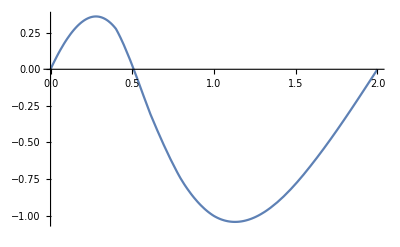

```mathematica
Plot[ysol[1][x],{x,0,L}]
```

```mathematica
tb=Table[Plot[ysol[t][x],{x,0,L},PlotRange->{-1.5,1.5}],{t,0,4,.05}];
```

```mathematica
ListAnimate[%]
```

```mathematica
τ[x_]= Integrate[1/c[x1],{x1,0,x},Assumptions->x>0]
```

Log[1+x]

```mathematica
ψWKB[n_,x_]=Sqrt[c[x]] Sin[n Pi τ[x]/τ[L]]
```

√(1+x) Sin[2.8596 n Log[1+x]]

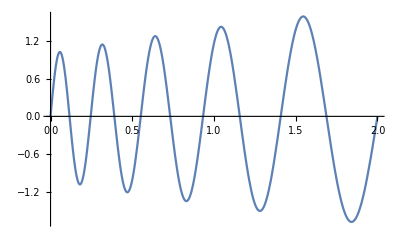

```mathematica
Plot[ψWKB[10,x],{x,0,L}]
```

```mathematica
sol[ω_]:= NDSolve[{c[x]^2 ψ''[x]==-ω^2ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,0,L}]
```

```mathematica
ψend[ω_]:= (ψ[L]/.sol[ω][[1]])/; ω∈ Reals
```

```mathematica
ψend[ω]
```

ψend[ω]

```mathematica
ψend[1.]
```

1.62849

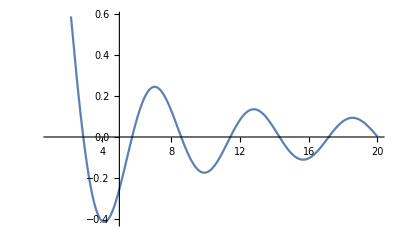

```mathematica
Plot[ψend[ω],{ω,1,20}]
```

```mathematica
ωWKB[n_]= n Pi/τ[L]
```

2.8596 n

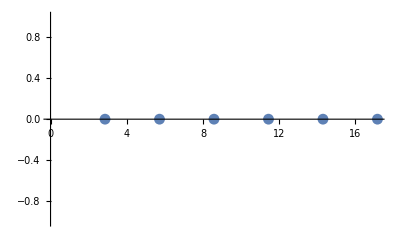

```mathematica
ListPlot[Table[{ωWKB[n],0},{n,1,6}]]
```

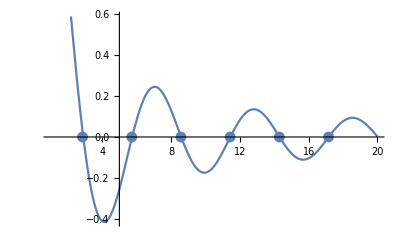

```mathematica
Show[%28,%]
```

```mathematica
ωs[n_]:=ωs[n]= ω/.FindRoot[ψend[ω]==0,{ω,ωWKB[n]}]
```

```mathematica
ψs[n_]:=ψs[n]= ψ/.sol[ωs[n]][[1]]
```

```mathematica
ψs[1]
```

InterpolatingFunction[{{0., 2.}}, <>]

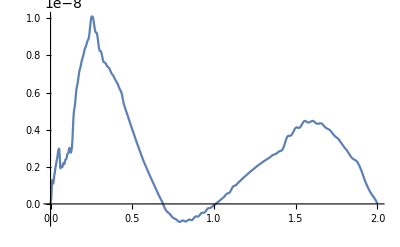

```mathematica
Plot[{ψs[2][x]-ψWKB[2,x]ψs[2][1.]/ψWKB[2,1.]}//Evaluate,{x,0,L}]
```

```mathematica
Table[{ωs[n],ωWKB[n]},{n,1,10}]
```

{{2.90298,2.8596},{5.74102,5.7192},{8.59336,8.5788},{11.4493,11.4384},{14.3067,14.298},{17.1649,17.1576},{20.0234,20.0172},{22.8823,22.8768},{25.7413,25.7364},{28.6004,28.596}}

```mathematica
TableForm[%]
```

2.90298 | 2.8596
5.74102 | 5.7192
8.59336 | 8.5788
11.4493 | 11.4384
14.3067 | 14.298
17.1649 | 17.1576
20.0234 | 20.0172
22.8823 | 22.8768
25.7413 | 25.7364
28.6004 | 28.596

```mathematica
ω[n_]:= ωWKB[n]/; n>10
```

```mathematica
ω[n_]:= ωs[n]/; n≤ 10
```

```mathematica
ψ[n_,x_]=ψWKB[n,x]
```

√(1+x) Sin[2.8596 n Log[1+x]]

```mathematica
A[n_]:= NIntegrate[ψ[n,x] y0[x]/c[x]^2,{x,0,L}]/NIntegrate[ψ[n,x]^2/c[x]^2,{x,0,L}]
```

```mathematica
A[3]
```

-0.22074

```mathematica
y[x_,t_]= Sum[A[n] Cos[ω[n] t] ψ[n,x],{n,1,15}]
```

0.359719 √(1+x) Cos[2.90298 t] Sin[2.8596 Log[1+x]]+0.624564 √(1+x) Cos[5.74102 t] Sin[5.7192 Log[1+x]]-0.22074 √(1+x) Cos[8.59336 t] Sin[8.5788 Log[1+x]]+0.0526929 √(1+x) Cos[11.4493 t] Sin[11.4384 Log[1+x]]-0.015434 √(1+x) Cos[14.3067 t] Sin[14.298 Log[1+x]]+0.00484357 √(1+x) Cos[17.1649 t] Sin[17.1576 Log[1+x]]-0.00205041 √(1+x) Cos[20.0234 t] Sin[20.0172 Log[1+x]]+0.000860683 √(1+x) Cos[22.8823 t] Sin[22.8768 Log[1+x]]-0.000475575 √(1+x) Cos[25.7413 t] Sin[25.7364 Log[1+x]]+0.000238804 √(1+x) Cos[28.6004 t] Sin[28.596 Log[1+x]]-0.000155361 √(1+x) Cos[31.4556 t] Sin[31.4556 Log[1+x]]+0.0000871055 √(1+x) Cos[34.3152 t] Sin[34.3152 Log[1+x]]-0.0000629151 √(1+x) Cos[37.1748 t] Sin[37.1748 Log[1+x]]+0.0000379528 √(1+x) Cos[40.0344 t] Sin[40.0344 Log[1+x]]-0.0000294488 √(1+x) Cos[42.894 t] Sin[42.894 Log[1+x]]

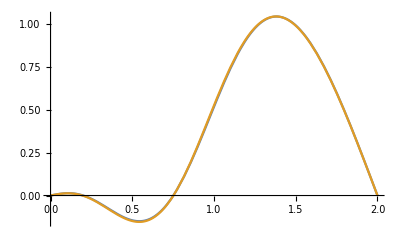

```mathematica
Plot[{y[x,4],ysol[4][x]},{x,0,L}]
```

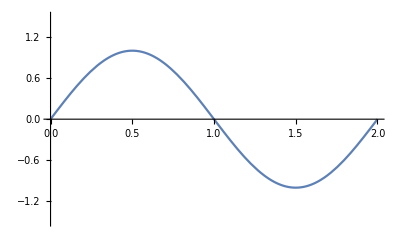
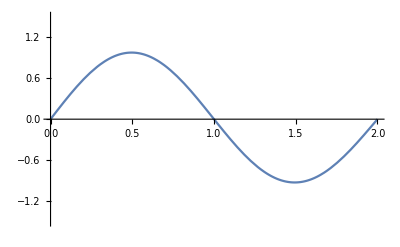
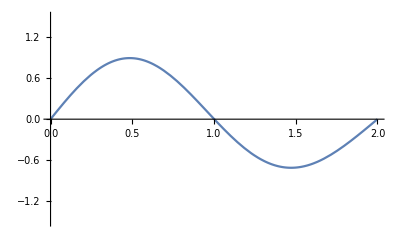
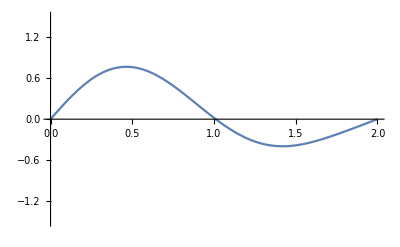
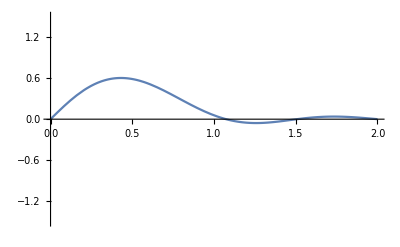
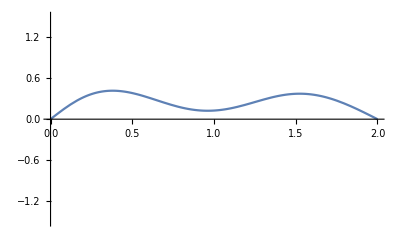
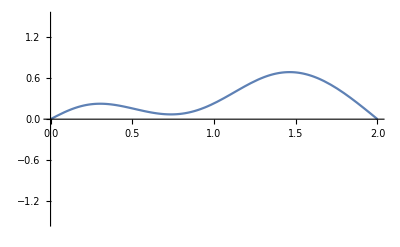
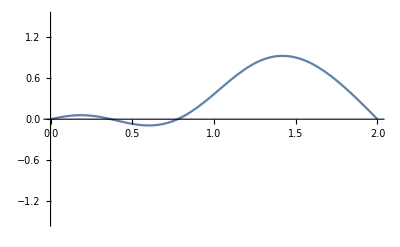

```mathematica
tb1=Table[Plot[y[x,t],{x,0,L},PlotRange->{-1.5,1.5}],{t,0,4,.05}]
```

```mathematica
ListAnimate[%]
```

```mathematica
ListAnimate[Table[Show[tb[[n]],tb1[[n]]],{n,1,Length[tb]}]]
```

```mathematica
ωs[1]
```

2.90298

```mathematica
ωs[2]
```

5.74102